#### Elementos de la representación matricial del Hamiltoniano LMG en la base |j,m) con ϵ =1, ℏ=1 y γy = 3γx

```mathematica
Hel[j_,m_,k_]:= m KroneckerDelta[m,k]-1/2(γx/(2j-1))(√(j(j+1)-m(m+1))√(j(j+1)-(m+1)(m+2))KroneckerDelta[m+2,k]+√(j(j+1)-m(m-1))√(j(j+1)-(m-1)(m-2))KroneckerDelta[m-2,k]-4(j(j+1)-m^2)KroneckerDelta[m,k])
```

De esta forma tarda mucho en armar la gráfica.

```mathematica
j=20;
Hmtrx= Table[Table[Hel[j,m,k],{m,j,-j,-1}],{k,j,-j,-1}];
```

```mathematica
EVls=Eigenvalues[Hmtrx];
```

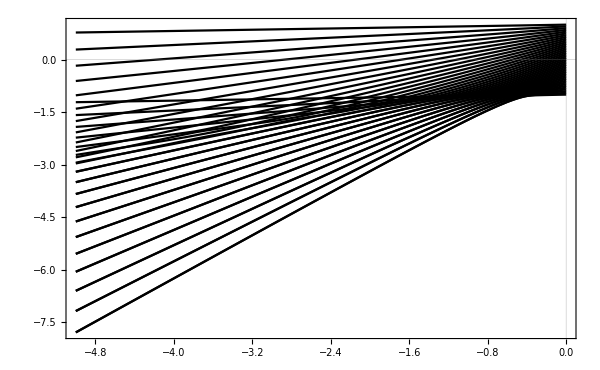

```mathematica
Plot[EVls/j,{γx,-5,0},PlotTheme->"Scientific",PlotRange->All,PlotStyle->Black]
```

## Forma alternativa:

#### 1. Se fija j=20 , se construye la matriz Hmtrx y se calculan sus valores propios.

```mathematica
j=20;
Hmtrx= Table[Table[Hel[j,m,k],{m,j,-j,-1}],{k,j,-j,-1}];
```

```mathematica
EVls=Eigenvalues[Hmtrx];
```

#### 2. Se define un rango que representa el |γx| (Es más rápido dependiendo el salto entre cada punto) y se define la lista de listas de puntos TempEvls, los cuales tienen la forma (Abs[γx],Ek[γx])

```mathematica
xrange = Range[0,5,0.01];
TempEVls =Table[Transpose[{xrange,Table[EVls[[i]]/j/.γx-> k,{k,0,-5,-0.01}]}],{i,1,2j+1}];
```

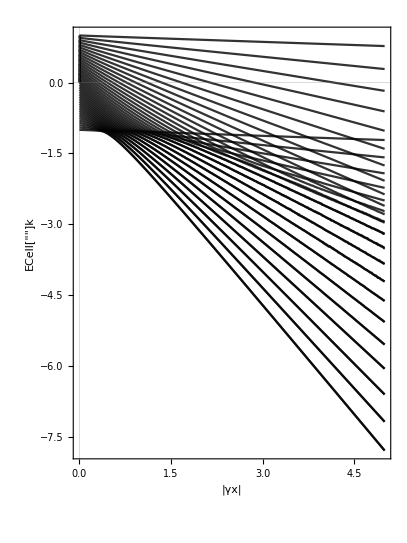

```mathematica
ListLinePlot[TempEVls,PlotRange->All,PlotStyle-> GrayLevel[0,0.8],PlotTheme->"Scientific",ImageSize->{360,480},AspectRatio->Full,FrameLabel->{{"ECell["",ExpressionUUID->"96a1e805-9fcc-4f8a-9f04-c2c6ba8bb60b"]k",None},{"|γx|",None}},LabelStyle->{FontFamily->"DejaVu Sans",GrayLevel[0]}]
```

## Aquí haré algunas pruebas para comparar con fortran

```mathematica
j=1;
Hmtrx1= Table[Table[Hel[j,m,k],{m,j,-j,-1}],{k,j,-j,-1}];
```

```mathematica
EVls1=Eigenvalues[Hmtrx1]
```

{4 γx,2 γx-√(1+γx^2),2 γx+√(1+γx^2)}

```mathematica
EVecs1=Eigenvectors[Hmtrx1 ]/. γx-> -5
```

{{0,1,0},{1/5 (1-√26),0,1},{1/5 (1+√26),0,1}}

```mathematica
EVecs1[[1]]
```

{0,1,0}

```mathematica
Table[Normalize[N[EVecs1[[i]]]],{i,1,3}]
```

{{0.,1.,0.},{-0.633989,0.,0.773342},{0.773342,0.,0.633989}}

```mathematica
N[EVls1/. γx-> -5]
```

{-20.,-15.099,-4.90098}

```mathematica
xrange1 = Range[0,5,0.01];
TempEVls1 =Table[Transpose[{xrange1,Table[EVls1[[i]]/j/.γx-> k,{k,0,-5,-0.01}]}],{i,1,2j+1}];
```

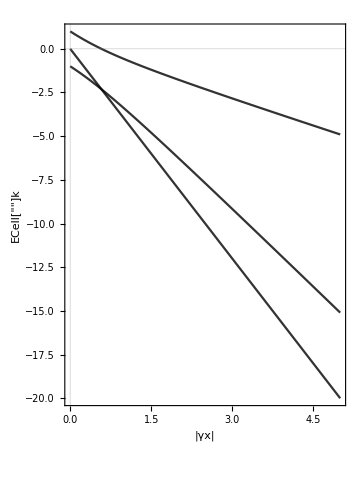

```mathematica
ListLinePlot[TempEVls1,PlotRange->All,PlotStyle-> GrayLevel[0,0.8],PlotTheme->"Scientific",ImageSize->{360,480},AspectRatio->Full,FrameLabel->{{"ECell["",ExpressionUUID->"c35a6bc1-15f8-4fd5-beb6-484e1959b1a7"]k",None},{"|γx|",None}},LabelStyle->{FontFamily->"DejaVu Sans",GrayLevel[0]}]
```

## Aquí vamos a tratar la representación de Husimi

La matriz hamiltoniana dependiente de γx para j=1 (Para un valor particular de γx. Sea γx=1)

```mathematica
MatrixForm[Hmtrx1]/. γx-> 1
```

(3 | 0 | -1
0 | 4 | 0
-1 | 0 | 1)

Se diagonaliza este Hamiltoniano para encontrar eigenvalores (Estos son los mismos que se imprimen en Fortran)

```mathematica
N[Eigenvalues[Hmtrx1]/. γx-> 1]
```

{4.,0.585786,3.41421}

Los eigenvectores son similares a los que imprime Fortran.

```mathematica
EigVals1=Table[Normalize[N[Eigenvectors[Hmtrx1]][[i]]/. γx-> 1],{i,1,3}]
```

{{0.,1.,0.},{0.382683,0.,0.92388},{-0.92388,0.,0.382683}}

El cálculo de la representación de Husimi se realiza para un estado k, una j fija. Debemos calcular Q(α)=|<α|Ek>|^2 = <α|Ek> <Ek |α>.

```mathematica
α[θ_,ϕ_]:=Tan[θ/2]Exp[-I ϕ];
```

Vamos a probar con k=2

```mathematica
C1=EigVals1[[2]]
```

{0.382683,0.,0.92388}

```mathematica
C1={{0.38268343236508984},{0.},{0.9238795325112867}}
```

{{0.382683},{0.},{0.92388}}

```mathematica
C2={{0.38268343236508984,0.,0.9238795325112867}}
```

{{0.382683,0.,0.92388}}

.b4